```mathematica
a1={{0.776237798,0.734968288},{0.92325633,0.869710542},{0.961849512,0.893551812}}
```

{{0.776238,0.734968},{0.923256,0.869711},{0.96185,0.893552}}

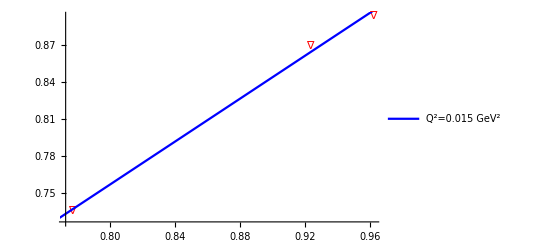

```mathematica
p1=Show[{ListPlot[a1,PlotStyle->Red,PlotMarkers->{"∇"},PlotTheme->"Monochrome"],Plot[0.059546444504782525+0.8715865450903035 x,{x,0,1},PlotStyle->{Blue},PlotLegends->{"Q^2=0.015 GeV^2"}]}]
```

```mathematica
a2={{0.762386729,0.721869516},{0.916791916,0.856000091},{0.959483677
,0.888522598}}
```

{{0.762387,0.72187},{0.916792,0.856},{0.959484,0.888523}}

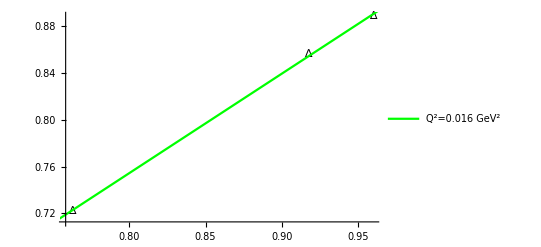

```mathematica
p2=Show[{ListPlot[a2,PlotStyle->Black,PlotMarkers->{"∆"},PlotTheme->"Monochrome"],Plot[0.07298855183435583+0.8517295035286946 x,{x,0,1},PlotStyle->{Green},PlotLegends->{"Q^2=0.016 GeV^2"}]}]
```

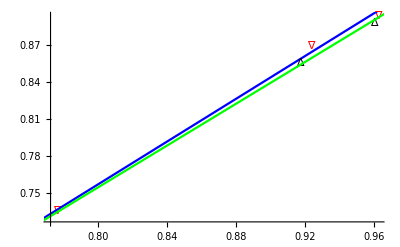

```mathematica
Show[p1,p2]
```

```mathematica
a3={{0.73880265,0.69331026},{0.913478093,0.849136135},{0.957002605,0.88842565}}
```

{{0.738803,0.69331},{0.913478,0.849136},{0.957003,0.888426}}

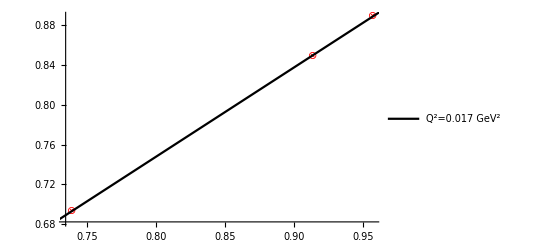

```mathematica
p3=Show[{ListPlot[a3,PlotStyle->Red,PlotMarkers->{"⊗"},PlotTheme->"Monochrome"],Plot[0.033073376079195194+0.8935985884973402 x,{x,0,1},PlotStyle->{Black},PlotLegends->{"Q^2=0.017 GeV^2"}]}]
```

```mathematica
a4={{0.474750239,0.438269957},{0.802237054,0.699082651},{0.899284834,0.772821715}}
```

{{0.47475,0.43827},{0.802237,0.699083},{0.899285,0.772822}}

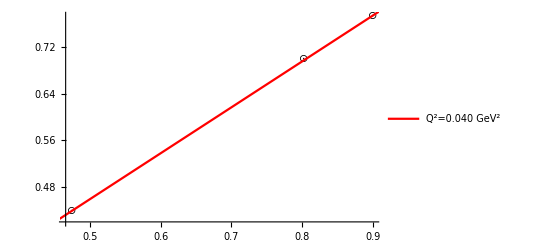

```mathematica
p4=Show[{ListPlot[a4,PlotStyle->Black,PlotMarkers->{"⊙"},PlotTheme->"Monochrome"],Plot[0.06351694136860286+0.790169334781078 x,{x,0,1},PlotStyle->{Red},PlotLegends->{"Q^2=0.040 GeV^2"}]}]
```

```mathematica
a5={{0.150702222,0.202149118},
{0.639154289,0.518383747},
{0.814106153,0.627541561},
{0.887475821,0.678748373},
{0.925328675,0.702290854}}
```

{{0.150702,0.202149},{0.639154,0.518384},{0.814106,0.627542},{0.887476,0.678748},{0.925329,0.702291}}

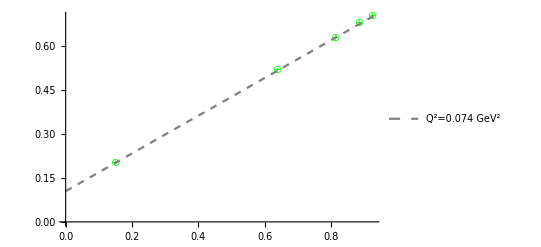

```mathematica
p5=Show[{ListPlot[a5,PlotStyle->Green,PlotMarkers->{"⊕"},PlotTheme->"Monochrome"],Plot[0.10501734741549378+0.6450620755563956 x,{x,0,1},PlotStyle->{Dashed,Gray},PlotLegends->{"Q^2=0.074 GeV^2"}]}]
```

```mathematica
a6={{0.125838232,0.186939927},
{0.805215656,0.619203536},
{0.922091045,0.69007286}}
```

{{0.125838,0.18694},{0.805216,0.619204},{0.922091,0.690073}}

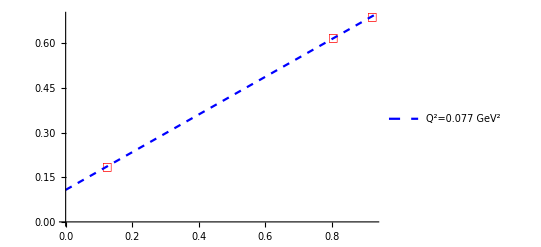

```mathematica
p6=Show[{ListPlot[a6,PlotStyle->Red,PlotMarkers->{"□"},PlotTheme->"Monochrome"],Plot[0.10748566506872526+0.6333877652481616 x,{x,0,1},PlotStyle->{Dashed,Blue},PlotLegends->{"Q^2=0.077 GeV^2"}]}]
```

```mathematica
a7=a={{0.763321203,0.565886107},
{0.855729087,0.615382608},
{0.931173637,0.657802906}}
```

{{0.763321,0.565886},{0.855729,0.615383},{0.931174,0.657803}}

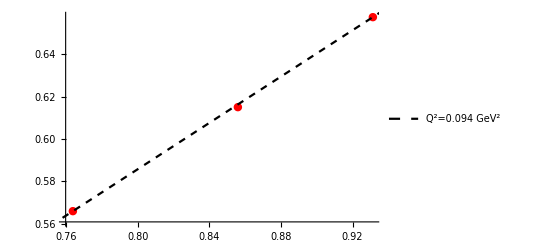

```mathematica
p7=Show[{ListPlot[a7,PlotStyle->Red,PlotMarkers->{"●"},PlotTheme->"Monochrome"],Plot[0.14789518478078584+0.5471621734406393 x,{x,0,1},PlotStyle->{Dashed,Black},PlotLegends->{"Q^2=0.094 GeV^2"}]}]
```

```mathematica
a8={{0.340512378,0.297691781},
{0.849921981,0.529905175},
{0.893168615,0.54173997}}
```

{{0.340512,0.297692},{0.849922,0.529905},{0.893169,0.54174}}

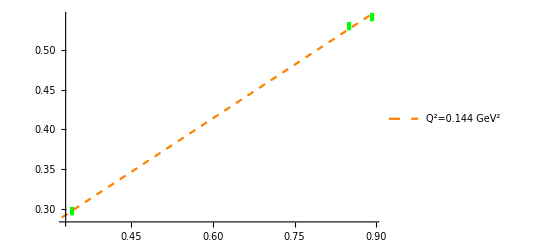

```mathematica
p8=Show[{ListPlot[a8, PlotStyle -> Green, PlotMarkers -> {"▮"}, 
   PlotTheme -> "Monochrome"], Plot[0.1455968108304168 +0.44756438973519597 x, {x, 0, 1}, PlotStyle -> {Dashed,Orange},PlotLegends->{"Q^2=0.144 GeV^2"}]}]
```

```mathematica
a9={{0.186407295,0.220078112},
{0.706164776,0.416980725},
{0.805285769,0.457386981}}
```

{{0.186407,0.220078},{0.706165,0.416981},{0.805286,0.457387}}

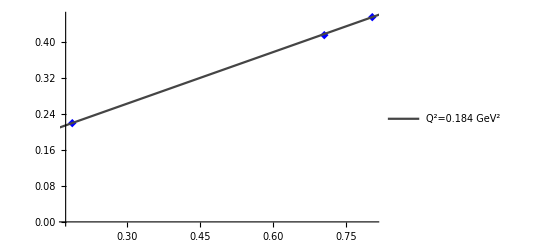

```mathematica
p9=Show[{ListPlot[a9,PlotStyle->Blue,PlotMarkers->{"◆"},PlotTheme->"Monochrome"],Plot[0.14866199467564004+0.38192822667242854 x,{x,0,1},PlotStyle->{GrayLevel[0.27]},PlotLegends->{"Q^2=0.184 GeV^2"}]}]
```

```mathematica
a10={{0.276967535,0.21830093},
{0.528766222,0.27755895},
{0.676012851,0.314962734}}
```

{{0.276968,0.218301},{0.528766,0.277559},{0.676013,0.314963}}

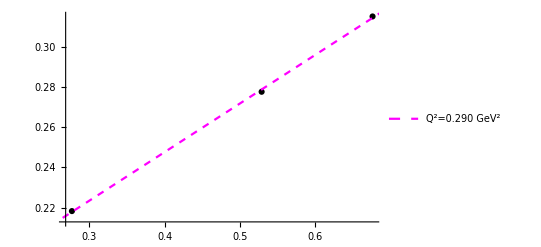

```mathematica
p10=Show[{ListPlot[a10,PlotStyle->Black,PlotMarkers->Automatic,PlotTheme->"Monochrome"],Plot[0.15099862467639966+0.24148983236329513 x,{x,0,1},PlotStyle->{Dashed,Magenta},PlotLegends->{"Q^2=0.290 GeV^2"}]}]
```

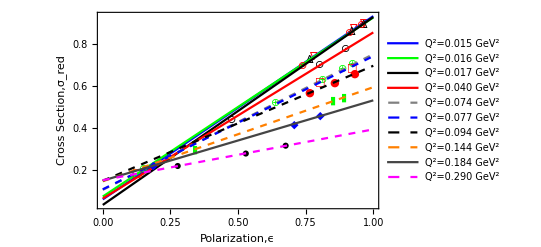

```mathematica
b=Show[p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,PlotRange->Automatic,FrameLabel->{"Polarization,ϵ","Cross Section,σ_red"},LabelStyle->{FontFamily->"Arial",22,GrayLevel[0],Bold},Axes->False,ImageSize->Full,Frame->True]
```

```mathematica
Export["Cross Section.png",b]
```

Cross Section.png